# discretization

## analytics

## derive eoms

### definitions

```mathematica
<<EDCRGTCcode.m;
xIN={r,t,x1,x2,x3};
g=Series[ DiagonalMatrix[{1/f[r], - f[r] ,r^2,r^2,r^2 }] + ϵ ⅇ^(-ⅈ ω t)SparseArray[ {{3,4}->  hxy[r], {4,3}->  hxy[r]} ,5 ] , {ϵ,0,1}];
RGtensors[g,xIN];
```

gdd = (1/f[r] | 0 | 0 | 0 | 0
0 | -f[r] | 0 | 0 | 0
0 | 0 | r^2 | ⅇ^(-ⅈ t ω) hxy[r] ϵ+O[ϵ]^2 | 0
0 | 0 | ⅇ^(-ⅈ t ω) hxy[r] ϵ+O[ϵ]^2 | r^2 | 0
0 | 0 | 0 | 0 | r^2)

LineElement = (r^2 d[x1]^2+r^2 d[x2]^2+r^2 d[x3]^2+d[r]^2/f[r]-d[t]^2 f[r])+2 ⅇ^(-ⅈ t ω) d[x1] d[x2] hxy[r] ϵ+O[ϵ]^2

gUU = (f[r]+O[ϵ]^3 | 0 | 0 | 0 | 0
0 | -1/f[r]+O[ϵ]^3 | 0 | 0 | 0
0 | 0 | 1/r^2+(ⅇ^(-2 ⅈ t ω) hxy[r]^2 ϵ^2)/r^6+O[ϵ]^3 | -(ⅇ^(-ⅈ t ω) hxy[r] ϵ)/r^4+O[ϵ]^2 | 0
0 | 0 | -(ⅇ^(-ⅈ t ω) hxy[r] ϵ)/r^4+O[ϵ]^2 | 1/r^2+(ⅇ^(-2 ⅈ t ω) hxy[r]^2 ϵ^2)/r^6+O[ϵ]^3 | 0
0 | 0 | 0 | 0 | 1/r^2+O[ϵ]^3)

gUU computed in 0.008729 sec

Gamma computed in 0.012277 sec

Riemann(dddd) computed in 0.065514 sec

Riemann(Uddd) computed in 0.139326 sec

Ricci computed in 0.066041 sec

Weyl computed in 0.326521 sec

Einstein computed in 0.027133 sec

All tasks completed in 0.662865 seconds

Einstein’s eqs

```mathematica
Einsdd = Rdd - 1/2 gdd R - 6  gdd;
```

### simplify eom

```mathematica
solnf = {f-> Function[r, r^2(1-rH^4/r^4) ]};
```

```mathematica
vars = {hxy''[r],hxy'[r],hxy[r], ω};
```

```mathematica
Simplify[Einsdd  /. ϵ-> 0 /. solnf ]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
repfPP = Solve[ Simplify[Einsdd[[3,3]]  /. ϵ-> 0  ]== 0 , f''[r] ][[1]];
```

```mathematica
eqaux = Collect[(-1/2 f[r])^-1 ⅇ^(ⅈ t ω)D[Einsdd[[3,4]], ϵ]  /. ϵ-> 0  /. repfPP , vars, Simplify]
```

hxy[r] (ω^2/f[r]^2-(2 f'[r])/(r f[r]))+(-1/r+f'[r]/f[r]) hxy'[r]+hxy''[r]

```mathematica
repr = {r-> rH/y, ω-> ω1 rH}; repfields = {hxy-> Function[x, hxy[rH/x] ]};
```

```mathematica
repfields2 = {hxy-> Function[y, (1- y^2)^(-ⅈ ω1 /4) h[y] ]};
```

```mathematica
Collect[rH^2 y^-2(1- y^2)^(ⅈ ω1 /4) eqaux /. solnf /. repr /. repfields  /. repfields2 , {h''[y], h'[y], h[y], ω1 }, Simplify ]
```

((4 (1+y^4))/(-1+y^4)-(ⅈ y^2 (1+2 y^2) ω1)/(-1+y^4)-(y^2 (4+3 y^2+y^4) ω1^2)/(4 (-1+y^2) (1+y^2)^2)) h[y]+((y (-1+5 y^4))/(-1+y^4)-(ⅈ y^3 ω1)/(-1+y^2)) h'[y]+y^2 h''[y]

## numerics

## preliminaries

### import eoms

```mathematica
eqLinAUX =  ((4 (1+y^4))/(-1+y^4)-(ⅈ y^2 (1+2 y^2) ω1)/(-1+y^4)-(y^2 (4+3 y^2+y^4) ω1^2)/(4 (-1+y^2) (1+y^2)^2)) h[y]+((y (-1+5 y^4))/(-1+y^4)-(ⅈ y^3 ω1)/(-1+y^2)) h'[y]+y^2 h''[y];
```

```mathematica
eqLin =  eqLinAUX/. ω1-> λp // Together // Numerator // Simplify;
```

```mathematica
IRbc = Collect[ Series[ eqLin /. y-> 1- x , {x,0,0} ],x, Simplify ] /. f_[1]-> f[y];
UVbc = h[y];
```

### grids

```mathematica
Off[Part::pkspec1]
Off[LinearSolve::luc]
```

#### Cheb grid and d1

```mathematica
ChebGrid[xp_,xm_,nn_]:= Module[{ys,a,diag,d1,d2} ,

ys = Table[1/2(xp + xm) + 1/2(xp - xm) Cos[(π (i-1))/nn], {i,1,nn+1}];
d1= NDSolve`FiniteDifferenceDerivative[Derivative[1],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];
d2= NDSolve`FiniteDifferenceDerivative[Derivative[2],{ys},"DifferenceOrder"->"Pseudospectral"]["DifferentiationMatrix"];

{ys,d1,d2}

];
```

### input eoms

```mathematica
eqaux[0]=eqLin;
eqaux[1]=UVbc;
eqaux[2]=IRbc;
```

```mathematica
RepLin =  { h-> Function[{y},δϕ[y]  ] };

 For[ i=0,i≤ 2,i++, For[ orp = 0, orp≤ 2 , orp ++, 
eqlin[i][orp]= Evaluate[1/(orp!)D[ eqaux[i] , {λp,orp } ] ]/. λp-> 0  /. RepLin;
];
];


Clear[i,j,orp]
```

### module to compute the coefficients

```mathematica
ParseCoeffModule[nn_]:= Module[ {orp, Coeff, CoeffData,i,j,k,reps,ysT,d1y,d2y},

reps = {};
{ysT, d1y,d2y}= ChebGrid[0.,1.,nn];

(* Read off coefficients *)
For[ orp = 0, orp≤ 2 , orp ++,For[ i=0,i≤ 2,i++, 
(* [derivative][order of λp][bndy location] *)
	        Coeff[3][orp][i]= D[eqlin[i][orp], D[D[δϕ[y], y], y]] /. reps;
	        Coeff[2][orp][i]= D[eqlin[i][orp], D[δϕ[y], y]] /.reps;
	        Coeff[1][orp][i]= D[eqlin[i][orp], δϕ[y] ]/. reps ;

];
];

(* we use the replacement y-> ygrid *)
Table[ Evaluate[ Coeff[i][orp][j]/. y-> ysT  ]*ConstantArray[1,nn+1],{i,1,3} ,{orp,0,2}, {j,0,2}]

];
```

### module to implement bcs

```mathematica
DataWithBc[nn_][CoeffData_]:= Module[{CoeffDataBC},

CoeffDataBC = CoeffData[[1]];
CoeffDataBC[[1]]= CoeffData[[2,1]];
CoeffDataBC[[nn+1]]= CoeffData[[3,nn+1]];

CoeffDataBC

];
```

### module to find QNM

```mathematica
FindQNM[nn_]:= Module[ {AllCoeff,L2,OP,ParseCoeffAux,ysT,d1y,d2y,Id,orp,LL0,LL1 , j}, 

ParseCoeffAux =ParseCoeffModule[nn];

{ysT, d1y,d2y}= ChebGrid[0.,1.,nn];
Id =IdentityMatrix[nn+1];

For[ orp = 0, orp≤ 2 , orp ++, 
AllCoeff[orp][1] =   DataWithBc[nn][ParseCoeffAux[[1,orp+1]]];
AllCoeff[orp][2] =   DataWithBc[nn][ParseCoeffAux[[2,orp+1]]];
AllCoeff[orp][3] =   DataWithBc[nn][ParseCoeffAux[[3,orp+1]]];

OP[orp] = AllCoeff[orp][3]*d2y + AllCoeff[orp][2]*d1y + AllCoeff[orp][1]*Id; 
];

LL0 =  ArrayFlatten[({{OP[1], OP[0]}, {-Id, 0.}})]  // N;
LL1= ArrayFlatten[({{OP[2], 0.}, {0., Id}}) ] //N;

Eigensystem[{LL0,-LL1}]

 ];
```

## solution

```mathematica
SolnTest1 =FindQNM[20];
```

this gives a good approximation for the first 4 pairs of QNM, c.f. hep-th/0207133

```mathematica
7.18799
```

```mathematica
SolnTest1[[1]][[-6;;]] // ReIm   // Reverse
```

{{3.11945,-2.74668},{-3.11945,-2.74668},{5.16952,-4.76357},{-5.16952,-4.76357},{7.188,-6.76966},{-7.188,-6.76966}}

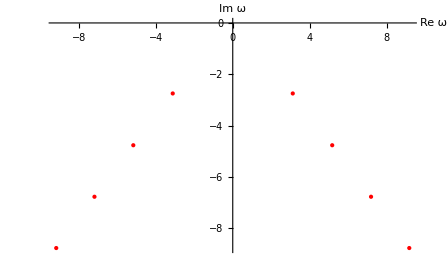

```mathematica
ListPlot[ ReIm[  SolnTest1[[1]][[-8;;]] ] , PlotStyle->{Red, PointSize[Large]} , AxesLabel->{"Re ω", "Im ω"}, BaseStyle->16]
```